# Explicación Poincaré

### Del oscilador armónico simple

Supongamos que tenemos un oscilador armónico

(d^2 x(t))/dt^2 = - k x(t)

-Graphics-

Su órbita (gráfica de la posición) es

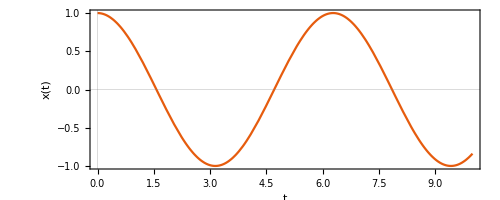

```mathematica
sol=NDSolve[
{x''[t]+x[t]==0,x[0]==1,x'[0]==0},x,{t,0,10}
][[1,1]];

ParametricPlot[Evaluate[{t,x[t]}/.sol],{t,0,10},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"t","x(t)"}]
```

El estado del sistema en cualquier instante está determinado por un punto en el espacio fase.

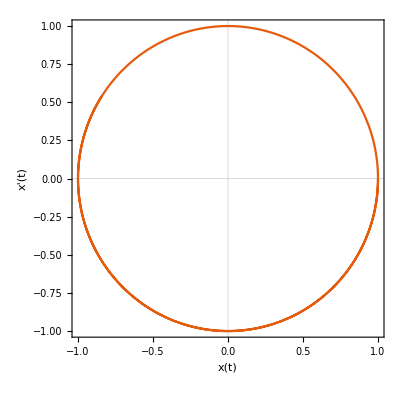

```mathematica
ParametricPlot[Evaluate[{x[t],x'[t]}/.sol],{t,0,10},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"x(t)","x'(t)"}]
```

Ahora, la pregunta es, ¿son necesarios todos los puntos de espacio fase para dar una descripción completa de la dinámica del sistema? Podemos notar que la órbita es periódica con periodo 2π, de manera que tomando el punto del espacio fase que ocurre cada intervalo de tiempo 2π tendremos una descripción del sistema a partir de la cual podemos reconstruir toda la dinámica, es decir, no se pierde información.

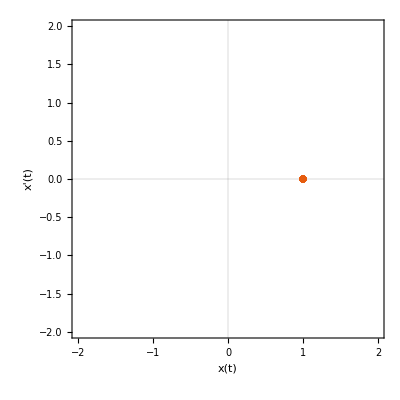

```mathematica
data=Reap[
NDSolve[
{x''[t]+x[t]==0,x[0]==1,x'[0]==0,WhenEvent[Mod[t,2π]==0,Sow[{x[t],x'[t]}]]},
x,
{t,0,100},
MaxSteps->∞
]
][[2,1]];
ListPlot[data,AspectRatio->1,PlotTheme->"Scientific",FrameLabel->{"x(t)","x'(t)"},PlotRange->{{-2,2},{-2,2}}]
```

### Del oscilador de Duffing

En ejemplo con una dinámica mucho más interesante es el oscilador de Duffing que físicamente puede representar un tipo de oscilador excitado bajo el amortiguamiento de un campo magnético. Este tipo de oscilador se presenta también en algunos sistemas electrónicos. Independientemente de su forma física la estructura matemática que describe su dinámica es una ecuación diferencial no lineal
-Graphics-

x^(..)(t) + δ ẋ(t) + α x(t) + β (x(t))^3 = γ Cos (ω t)

Esta ecuación no tiene solución analítica, y en su órbita presenta una dinámica muy compleja.

-Graphics-
-Graphics-

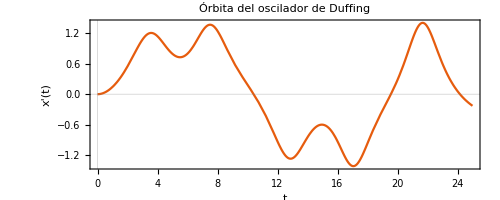

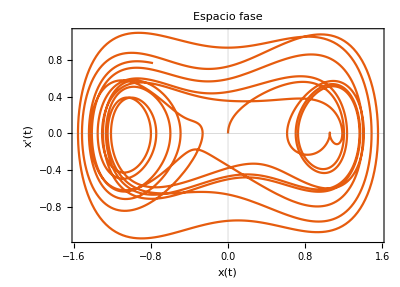

```mathematica
sol=Module[{δ=0.15,γ=0.3},
NDSolve[
{x''[t]+δ x'[t]-x[t]+x[t]^3==γ Cos[t],x[0]==0,x'[0]==0},x,{t,0,100},MaxSteps->∞
]
][[1,1]];
datasmall=Block[{δ=0.15,γ=0.3},
Reap[
NDSolve[
{x''[t]+δ x'[t]-x[t]+x[t]^3==γ Cos[t],x[0]==0,x'[0]==0,WhenEvent[Mod[t,2 π]==0,Sow[{x[t],x'[t]}]]},{},{t,0,100},MaxSteps->∞
]
]
][[-1,1]];
SetOptions[{Plot,ListPlot,ParametricPlot},BaseStyle->{FontSize->14}];
ParametricPlot[Evaluate[{t,x[t]}/.sol],{t,0,25},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"t","x'(t)"},PlotLabel->"Órbita del oscilador de Duffing"]
ParametricPlot[Evaluate[{x[t],x'[t]}/.sol],{t,0,100},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"x(t)","x'(t)"},PlotLabel->"Espacio fase"]
```

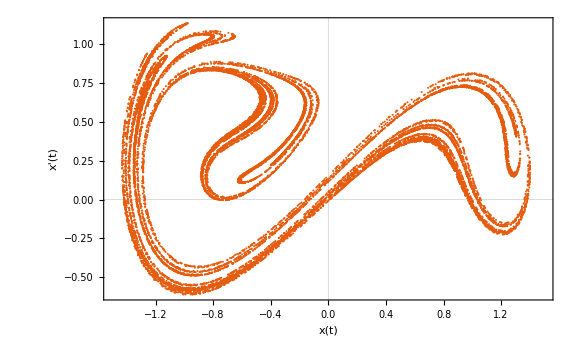

```mathematica
data=Block[{δ=0.15,γ=0.3},
Reap[
NDSolve[
{x''[t]+δ x'[t]-x[t]+x[t]^3==γ Cos[t],x[0]==0,x'[0]==0,WhenEvent[Mod[t,2π]==0,Sow[{x[t],x'[t]}]]},{},{t,0,100000},MaxSteps->∞
]
]
][[-1,1]];
ListPlot[data,ImageSize->Large,PlotRange->{{-1.5,1.5},All},PlotStyle->PointSize[0.0025],FrameLabel->{"x(t)","x'(t)"},PlotTheme->"Scientific"]
```

### 3 cuerpos revisited

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

A continuación se muestra una implementación de la dinámica del problema de 3 cuerpos restringido.

```mathematica
Manipulate[
Column[{
Row[{Dynamic[vxy0],Dynamic[xy0]}],
Row[{
threeBodyTrajectories[{Dynamic[vxy0],Dynamic[xy0]},vxy0,μ, T,ImageSize->{350,350}] ,
threeBodyPoincare[{Dynamic[vxy0],Dynamic[xy0]},vxy0,μ, T] 
}]
}],
{{T,20,"Tiempo"},10, 1000},
{{μ,1},0.01,10},
{{vxy0,{-0.5,-0.5}},{-2,-2},{2,2},ControlType->None},
{{xy0,{0.5,0.5}},{-2,-2},{2,2},ControlType->None},
ControlPlacement->{Top,Top,Top,Top,Top,Left,Left,Left},
Initialization:>(
threeBodyTrajectories[{Dynamic[vxy0_], Dynamic[xy0_]},
{vx0_,vy0_},μ_,T_,
plotOptions___] := 
Module[{nds,Tmax,prolog,funsToPlot,x0,y0},
{x0,y0}=xy0;
nds=NDSolve[
{x'[t]==vx[t],
y'[t]==vy[t],
vx'[t]==2 vy[t]+x[t]-((1-μ) (x[t]+μ))/(((x[t]+μ)^2+y[t]^2)^(3/2))-(μ (x[t]-1+μ))/(((x[t]-1+μ)^2+y[t]^2)^(3/2)),
vy'[t]==-2 vx[t]+y[t]-((1-μ) y[t])/(((x[t]+μ)^2+y[t]^2)^(3/2))-(μ y[t])/(((x[t]-1+μ)^2+y[t]^2)^(3/2)),

x[0]==x0,y[0]==y0,
vx[0]==vx0,vy[0]==vy0},
{x,y,vx,vy},{t,0,T}] // Quiet;

funsToPlot={x[t],y[t]}/. nds[[1]];
prolog = {PointSize[0.03],Transpose[{{RGBColor[1,.2,0],RGBColor[.5,.8,0]},{Point[{-0.5,0}],Point[{0.5,0}]}}]};
Show[ParametricPlot[Evaluate[funsToPlot],{t,0,T},
Prolog->prolog,
PlotStyle->{RGBColor[1,.2,0],RGBColor[.5,.8,0],RGBColor[.2,.6,1]},PlotRange->{{-2,2},{-2,2}},AspectRatio -> 1, MaxRecursion->ControlActive[3,9],plotOptions,PlotTheme->"Scientific", FrameLabel->{"x","y"},PlotLabel->"Órbita"],Graphics[{Dashed,RGBColor[.2,.6,1],Dynamic[Arrow[{xy0,xy0+vxy0}]],Locator[Dynamic[xy0+vxy0,(vxy0=#-xy0)&],Graphics[{Point[{0,0}]},ImageSize->10]],Locator[Dynamic[xy0]]}]]
];

threeBodyPoincare[{Dynamic[vxy0_], Dynamic[xy0_]},
{vx0_,vy0_},μ_,T_,
plotOptions___] := 
Module[{data,Tmax,prolog,funsToPlot,x0,y0},
{x0,y0}=xy0;
data=Reap[
NDSolve[
{
x'[t]==vx[t],
y'[t]==vy[t],
vx'[t]==2 vy[t]+x[t]-((1-μ) (x[t]+μ))/(((x[t]+μ)^2+y[t]^2)^(3/2))-(μ (x[t]-1+μ))/(((x[t]-1+μ)^2+y[t]^2)^(3/2)),
vy'[t]==-2 vx[t]+y[t]-((1-μ) y[t])/(((x[t]+μ)^2+y[t]^2)^(3/2))-(μ y[t])/(((x[t]-1+μ)^2+y[t]^2)^(3/2)),

x[0]==x0,y[0]==y0,
vx[0]==vx0,vy[0]==vy0,
WhenEvent[y[t] == 0 && y'[t] > 0,Sow[{x[t],vx[t]}]]
},
{x,y,vx,vy},{t,0,T}] // Quiet;
];

ListPlot[data[[2,1]],ImageSize->Medium,PlotTheme->"Scientific", FrameLabel->{"x(t)","x'(t)"}, PlotLabel->"Mapa de Poincaré",PlotRange->Full]
];
)]
```